# Impact of Parameter Perturbation on the Neural Network Performance

This project investigates the impact of perturbing parameters of a trained neural network on its performance by adding random noise drawn from different distributions to each layer. My project addresses the fundamental question: “How sensitive is the neural network to perturbations?”

## Introduction

to observe the effects of perturbing the weights and biases of the neural network. It

## The LeNet Model1

### Introduction

LeNet Model is a convolutional neural network for image classification developed by Yann LeCun and his collaborators at AT&T Bell Labs. It is known to have achieved a significantly high performance with an error rate less than 1% per each handwritten digit. LeCun’s work is known to be the first attempt to successfully train CNNs using gradient-based optimization.

```mathematica
leNet = NetModel["LeNet Trained on MNIST Data"]
```

NetChain[<11>]

### Architecture

LeNet comprises two main parts: two convolutional layers with max pooling for feature extraction and two fully connected layers for classification. Below are the summary graphics showing the architecture of the LeNet.

```mathematica
Information[leNet,"FullSummaryGraphic"]
```

-Graphics-

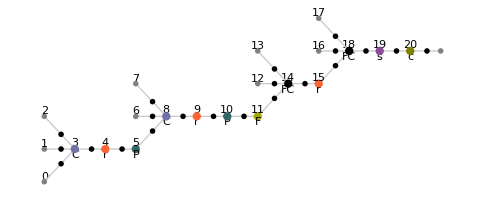

```mathematica
Information[ NetModel["LeNet Trained on MNIST Data"],"MXNetNodeGraphPlot"]
```

## The MNIST Dataset2

The LeNet is was trained on the MNIST dataset of handwritten digits and is known to have achieved 98.5% accuracy on the MNIST test dataset.

### Importing MNIST Test Dataset

The MNIST database consists of a training set of 60,000 examples and a test set of 10,000 examples.

```mathematica
mnistTest = ResourceData["MNIST","TestData"];
```

## Exploratory Data Analysis (EDA)

## Extracting the Weights of the LeNet

We extract the weights from the LeNet for each layer. The 1st (Convolutional), 4th (Convolutional), 8th (Linear) and 10th (Linear) layers have weights.

```mathematica
layerWeights = Table[NetExtract[leNet, {n, "Weights"}], {n, {1, 4, 8, 10}}]
```

{NumericArray[…],NumericArray[…],NumericArray[<500,800>, Real32],NumericArray[…]}

## Summary Statistics of Weight Distribution

### Graphical Summary

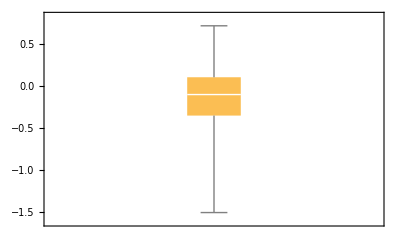
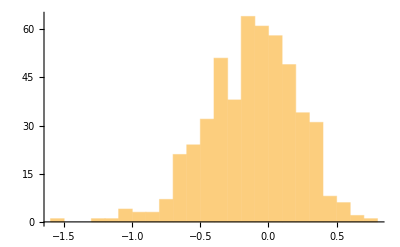
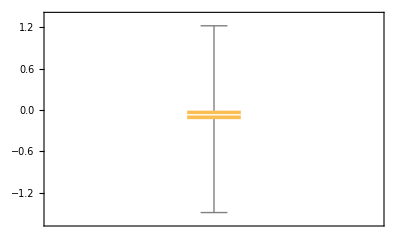
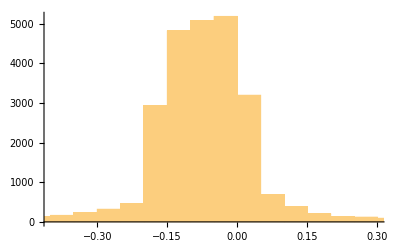
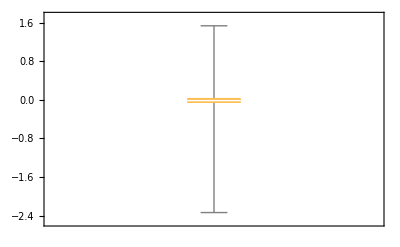
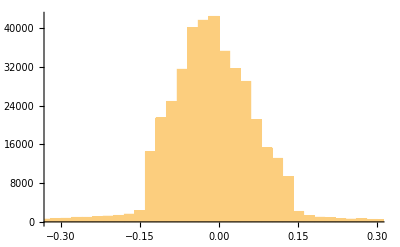
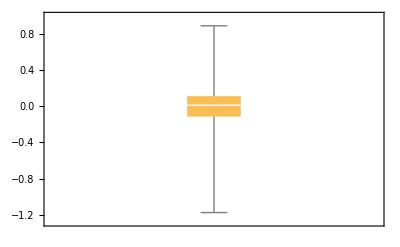
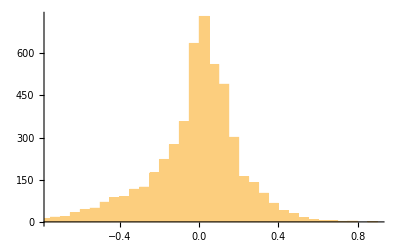
Weights Distribution
Layer 1
(Convolutional) | -Graphics- | -Graphics-
Layer 4
(Convolutional) | -Graphics- | -Graphics-
Layer 8
(Linear) | -Graphics- | -Graphics-
Layer 10
(Linear) | -Graphics- | -Graphics-

```mathematica
Grid[
{
{Style["Weights Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Table[{BoxWhiskerChart[Flatten[layerWeights[[l]]//Normal]],Histogram[Flatten[layerWeights[[l]]//Normal]]},{l,1,4}],
	TableHeadings->{{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}]}
},
Spacings->{2,1}
]
```

### Numerical Summary

```mathematica
Grid[
{{Style["Weights Distribution",FontSize->20, FontWeight->Bold]},
{TableForm[Transpose[Table[
{
Mean[Flatten[layerWeights[[l]]//Normal]],
StandardDeviation[Flatten[layerWeights[[l]]//Normal]],
Min[Flatten[layerWeights[[l]]//Normal]],
Max[Flatten[layerWeights[[l]]//Normal]],
Median[Flatten[layerWeights[[l]]//Normal]],
(Max[Flatten[layerWeights[[l]]//Normal]]-Min[Flatten[layerWeights[[l]]//Normal]]),
InterquartileRange[Flatten[layerWeights[[l]]//Normal]]
},
{l,1,4}
]],
TableHeadings->{{"Mean","Standard Deviation","Min","Max","Median","Range","IQR"},{"Layer 1\n(Convolutional)","Layer 4\n(Convolutional)","Layer 8\n(Linear)","Layer 10\n(Linear)"}}
]}},
Spacings->{2,1}
]
```

Weights Distribution
 | Layer 1
(Convolutional) | Layer 4
(Convolutional) | Layer 8
(Linear) | Layer 10
(Linear)
Mean | -0.1234 | -0.075064 | -0.0162563 | -0.019502
Standard Deviation | 0.332887 | 0.150124 | 0.117813 | 0.226538
Min | -1.5101 | -1.49051 | -2.33753 | -1.17305
Max | 0.720769 | 1.22129 | 1.53562 | 0.885933
Median | -0.10042 | -0.0711243 | -0.0159563 | 0.0103053
Range | 2.23087 | 2.7118 | 3.87316 | 2.05898
IQR | 0.457827 | 0.123344 | 0.104697 | 0.225497

## Analysis

We can see from the histograms that the distributions of the weights are roughly symmetrical around the center without any significant skewness. The peak is at the centre of the distribution around which most data points live.  Also, the mean and median of each distribution are strikingly close to each other, indicating that the distribution is not skewed to any one side. 

All four layers have means that are less than and very close to zero. 

The first layer is the most spread out among the four layers as we can see on the histogram and box plot. It has the most standard deviation and IQR, which means the average distance of each data point from the mean and median is relatively greater than other layers.

## Adding Noise to Weights in a Neural Network

## Random noise drawn from a uniform distribution

### Method

Now, we add noise to each weight of the LeNet for each layer with varying random value and then measure the performance of the perturb net by testing it on the MNIST test dataset. The following lines of code produce a  matrix where each row represents a varying range of random noise and each column represents each of the four layers.

where  and  are the possible minimum and maximum value of the noise added to the weights.

```mathematica
performanceMatrix1 = Table[
noisedWeights=NumericArray[(Normal[layerWeights[[l]]]+RandomReal[{-x,x},Dimensions[layerWeights[[l]]]])];
noisedNet=NetReplacePart[NetModel["LeNet Trained on MNIST Data"],{{1,4,8,10}[[l]],"Weights"}->noisedWeights];
ClassifierMeasurements[noisedNet, mnistTest,"Accuracy"],
{x,0.1,2,0.1},{l,1,4}];
```

### Result & Visualization

The following is a  heat map visualizes the distribution of the test accuracy of the perturbed LeNet as the range of random noise and the type of perturb layer vary. Each column represents a range of random noise and each row represents the specific layer perturbed. With each value in the heat map representing the test accuracy, greater value implies better performance and darker the color implies greater error rate on the test data.

```mathematica
xticks= Transpose[{
Range[4],
{"Cov 1","Cov 2","L1","L2"}
}];
yticks= Transpose[{
Range[20],
Table[StringTemplate["[-`n`~`n`]"][<|"n"->x|>],{x,0.1,2,0.1}]
}];
```

```mathematica
annotationLayer=MapThread[Inset[Style[#1,FontColor->If[#1<0.82,White,Black]],#2]&,
{Reverse/@Transpose[performanceMatrix1],Table[{i-1/2,j-1/2},{i,1,Dimensions[performanceMatrix1][[2]]},{j,1,Dimensions[performanceMatrix1][[1]]}]},2];
```

```mathematica
[]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

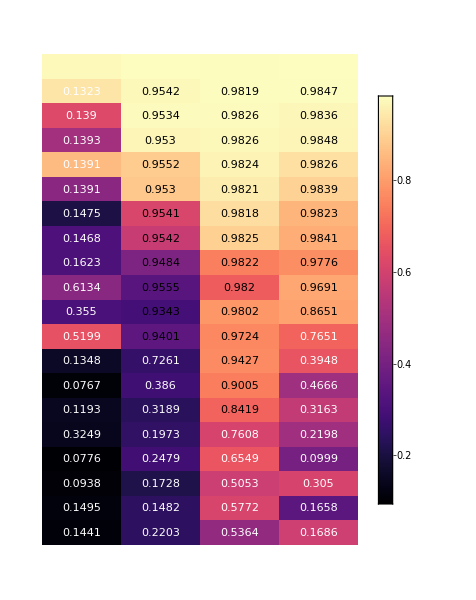

```mathematica
arrayPlot1=ArrayPlot[performanceMatrix1,
ColorFunction->"Magma",
FrameTicks->{yticks,xticks},
PlotLegends->Automatic,
FrameLabel->{"Noise Range","Layer"},
LabelStyle->12,
AspectRatio->3/2,
Epilog->annotationLayer]//Framed
```

```mathematica
ListPlot3D[performanceMatrix1]
```

-Graphics3D-

### Analysis

The first layer (convolutional) seems to be the most sensitive to perturbations as adding noise to this layer results in the worst damage to the performance of the neural net than perturbations to any other layers. While the second layer (convolutional) is slightly less sensitive than the first layer while perturbations to this layer has worse impacts on the performance of the neural net than the linear layers.

The fully connected linear layers are the relatively less sensitive to random noise since adding noise to them do not result in the worst performance of 10~20% test accuracy as the convolutional layers do. In particular, the third layer is very resistant to perturbations achieving over 50% test accuracy even when noise of great magnitude is added. 

Across all four layers, greater magnitude of the noise caused a severer damage to the performance of the model.

## Random noise drawn from a Gaussian distribution

### Method

In the previous section, we added noise randomly drawn from a uniform distribution. Now, we investigate how adding a noise randomly drawn from a Gaussian distribution that mimics the original weight distribution impacts the performance of the neural network. distrParams is a list that contains the mean and standard deviation of the weight distribution for each layer and these values are used to create Gaussian distributions that mimics the original distribution.

where  and  are the mean and standardard deviation of the weight distribution for each layer.

```mathematica
distrParams={{-0.1234,0.332887},{-0.075064,0.150124},{ -0.016256, 0.117813},{-0.019502, 0.332887}};
```

```mathematica
performanceMatrix2 = Table[
noisedWeights=NumericArray[(Normal[layerWeights[[l]]]+RandomVariate[NormalDistribution[distrParams[[l]][[1]],distrParams[[l]][[2]]*n],Dimensions[layerWeights[[l]]]])];
noisedNet=NetReplacePart[leNet,{{1,4,8,10}[[l]], "Weights"}->noisedWeights];
ClassifierMeasurements[noisedNet, mnistTest,"Accuracy"],
{n,Join[#^(-1)&/@ Reverse[Range[2,10,1]],Range[1,10,1]]},{l,1,4}];
```

### Result & Visualization

```mathematica
xticks= Transpose[{
Range[4],
{"Cov 1","Cov 2","L1","L2"}
}];
yticks= Transpose[{
Range[19],
Join[Table[StringTemplate["~(,/`n`)"][<|"n"->n|>],
	{n, Reverse[Range[2,10,1]]}],Table[StringTemplate["~(,`n`)"][<|"n"->n|>],
	{n,Range[1,10,1]}]]
}];
```

```mathematica
[]
```

{Magma,Inferno,Plasma,Viridis,EricsRdBuGnYl,EricsRdBuGnYl2,EricsPuBuGnYl,FakeParula,JoesBluGrnPnk2}

```mathematica
annotationLayer=MapThread[Inset[Style[#1,FontColor->If[#1<0.82,White,Black]],#2]&,{Reverse/@Transpose[performanceMatrix2],Table[{i-1/2,j-1/2},{i,1,Dimensions[performanceMatrix2][[2]]},{j,1,Dimensions[performanceMatrix2][[1]]}]},2];
```

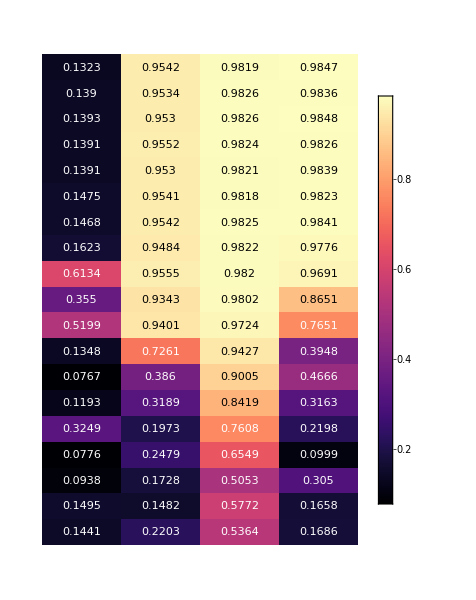

```mathematica
arrayPlot1=ArrayPlot[performanceMatrix2,
ColorFunction->"Magma",
FrameTicks->{yticks,xticks},
PlotLegends->Automatic,
FrameLabel->{"Noise Distribution","Layer"},
LabelStyle->12,
AspectRatio->3/2,
Epilog->annotationLayer]//Framed
```

```mathematica
ListPlot3D[performanceMatrix2]
```

-Graphics3D-

### Analysis

Like in the case of noise drawn from a uniform distribution, the most sensitive layer was the first layer, followed by the second, the fourth and the third layer in the order of sensitivity. 
The first layer is very sensitive to the noise drawn from a Gaussian distribution as it is to the uniform distribution, regardless of the standard deviation of the distribution. It performs relatively well (60% test accuracy) when the noise is drawn from a Gaussian distribution of the same standard deviation as the original weight distribution. On the other hand, the other three layers perform very well for small standard deviations and becomes worse as the layer standard deviations increase.

## Feature Representation

```mathematica
leNet
```

NetChain[<11>]

#### Input

```mathematica
inputImage=mnistTest[[7500]][[1]]
```

-Graphics-

```mathematica
3
```

```mathematica
inputVector=ImageData[inputImage];
```

```mathematica
inputVector//Dimensions
```

{28,28}

#### 1st Layer (Convolution)

```mathematica
outputL1=NetExtract[leNet,1][ArrayReshape[inputVector,{1,28,28}]];
```

```mathematica
noisedWeights1= Normal[NetExtract[leNet,{1,"Weights"}]]+ RandomReal[{-2.0,2.0}, Dimensions[NetExtract[leNet,{1,"Weights"}]]];
```

```mathematica
outputL1Noised= NetExtract[NetReplacePart[leNet,{1,"Weights"}->NumericArray[noisedWeights1]],1][ArrayReshape[inputVector,{1,28,28}]]
```

```mathematica
outputL1//Dimensions
```

{20,24,24}

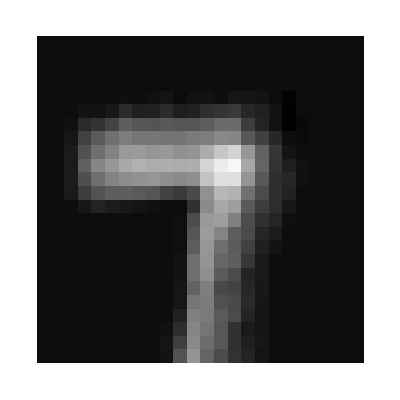
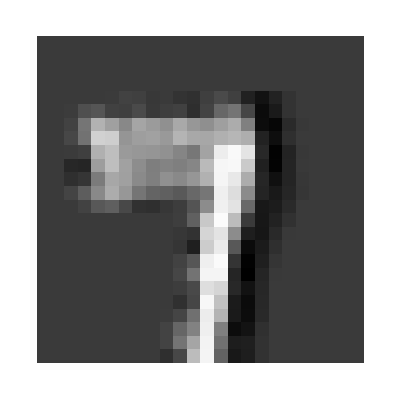
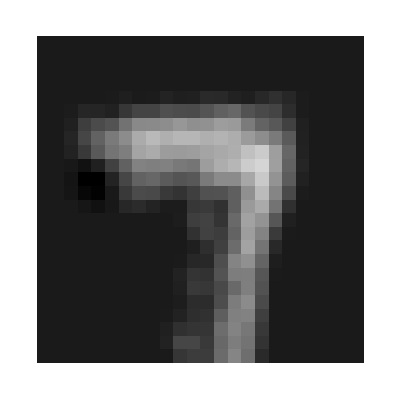
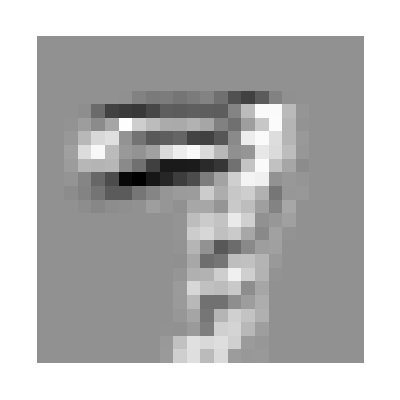
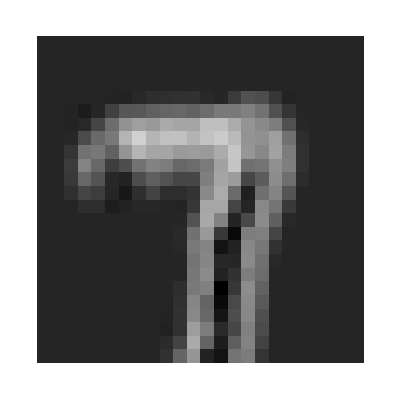
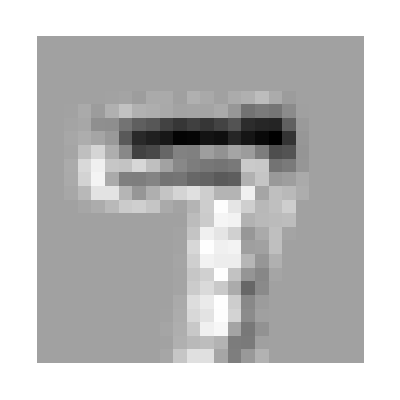
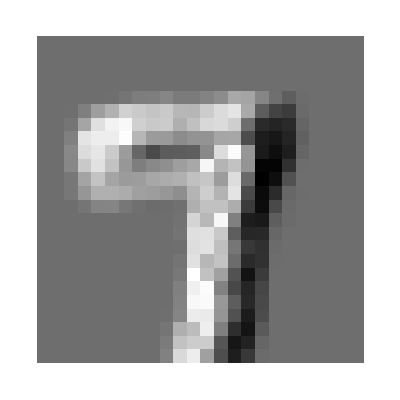
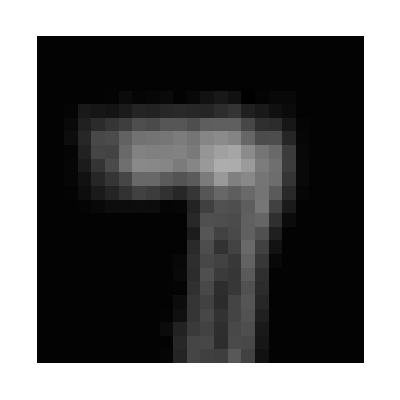
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{ArrayPlot/@ outputL1,ArrayPlot/@ outputL1Noised}]
```

#### 2nd Layer (ReLU)

```mathematica
outputL2=NetExtract[leNet,2][outputL1];
```

```mathematica
outputL2//Dimensions
```

{20,24,24}

```mathematica
outputL2Noised=NetExtract[leNet,2][outputL1Noised]
```

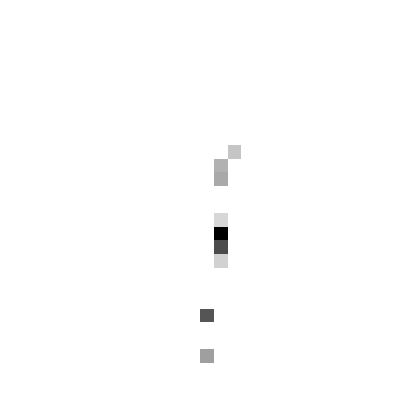
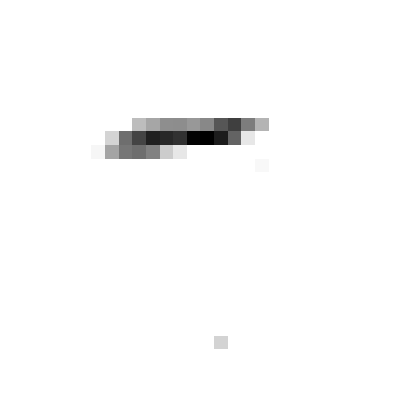
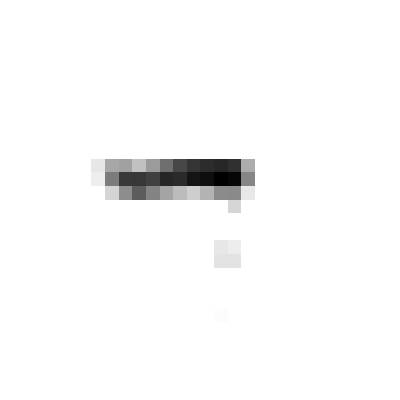
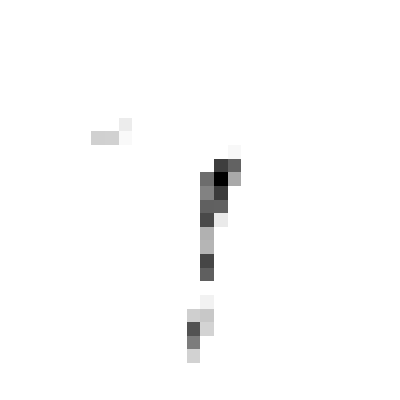
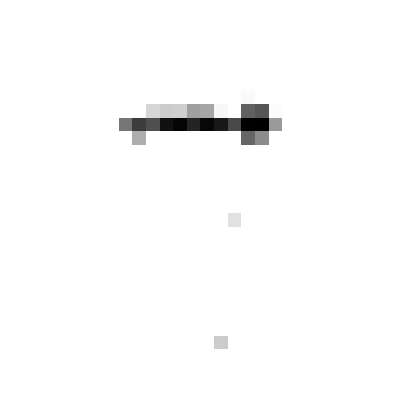
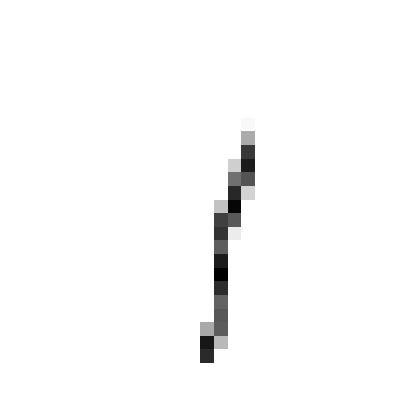
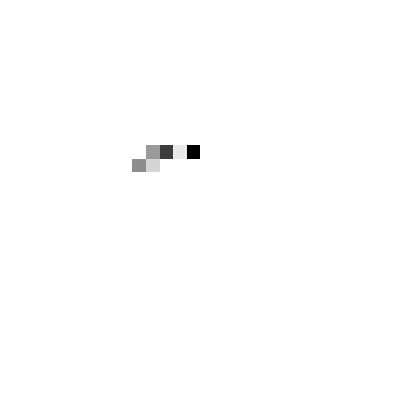
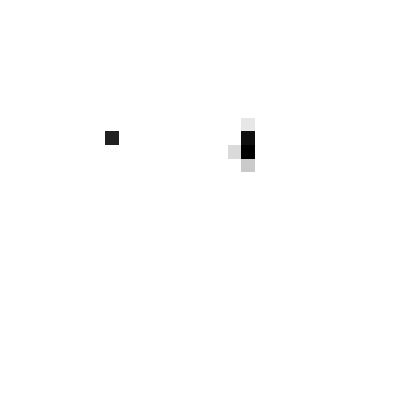
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{ArrayPlot/@outputL2,ArrayPlot/@outputL2Noised}]
```

#### 3rd Layer (Pooling)

```mathematica
outputL3=NetExtract[leNet,3][outputL2];
```

```mathematica
outputL3//Dimensions
```

{20,12,12}

```mathematica
outputL3Noised=NetExtract[leNet,3][outputL2Noised];
```

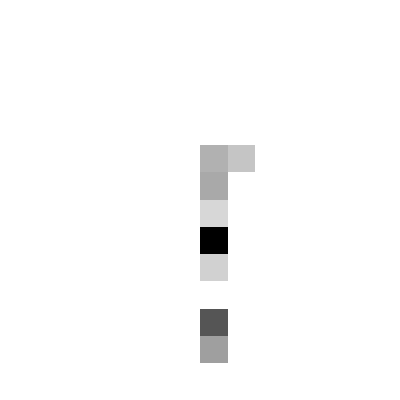
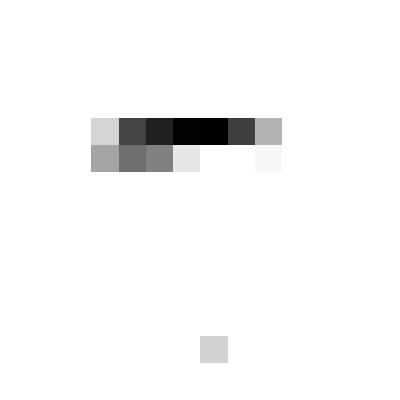
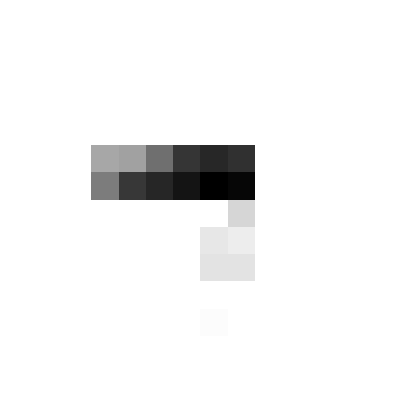
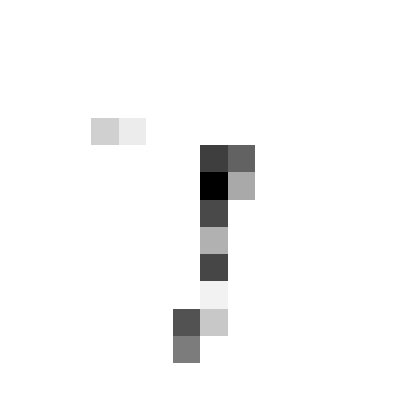
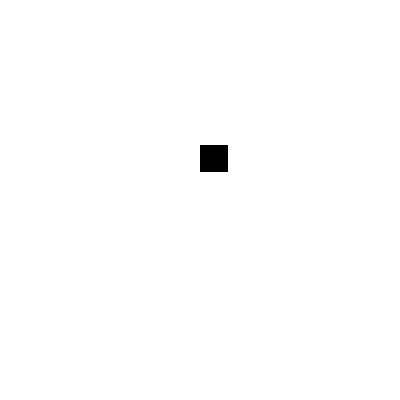
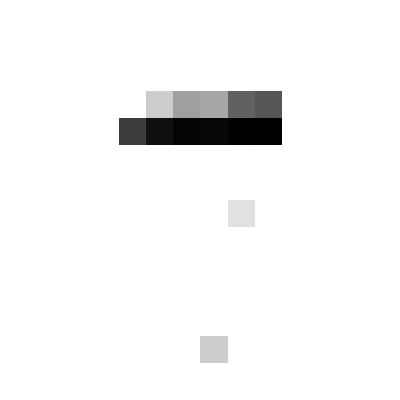
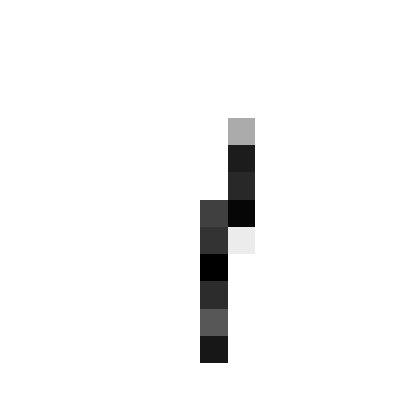
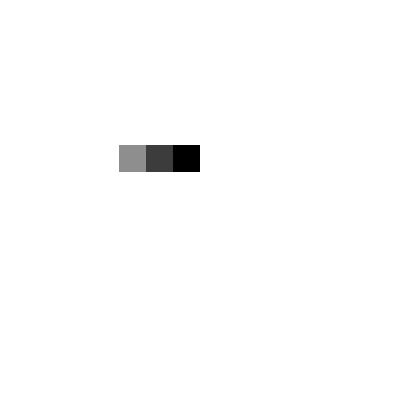
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{ArrayPlot/@outputL3,ArrayPlot/@outputL3Noised}]
```

#### 4th Layer (Convolution)

```mathematica
outputL4=NetExtract[leNet,4][outputL3];
```

```mathematica
outputL4//Dimensions
```

{50,8,8}

```mathematica
outputL4Noised=NetExtract[leNet,4][outputL3Noised];
```

```mathematica
Grid[{ArrayPlot/@ outputL4,ArrayPlot/@ outputL4Noised}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### 5th Layer (ReLU)

```mathematica
outputL5=NetExtract[leNet,5][outputL4];
```

```mathematica
outputL5//Dimensions
```

{50,8,8}

```mathematica
outputL5Noised=NetExtract[leNet,5][outputL4Noised];
```

```mathematica
Grid[{ArrayPlot/@ outputL5,ArrayPlot/@ outputL5Noised}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### 6th Layer (Pooling)

```mathematica
outputL6=NetExtract[leNet,6][outputL5];
```

```mathematica
outputL6//Dimensions
```

{50,4,4}

```mathematica
outputL6Noised=NetExtract[leNet,6][outputL5Noised];
```

```mathematica
Grid[{ArrayPlot/@ outputL6,ArrayPlot/@ outputL6Noised}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

#### 7th~10th Layer (Fully Connected)

```mathematica
fullyConnceted=NetChain[Table[NetExtract[leNet,n],{n,{7,8,9,10,11}}]]
```

NetChain[<5>]

```mathematica
fullyConnceted[outputL6]//NetDecoder[{"Class",{0,1,2,3,4,5,6,7,8,9}}]
```

7

```mathematica
fullyConnceted[outputL6Noised]//NetDecoder[{"Class",{0,1,2,3,4,5,6,7,8,9}}]
```

8

## Conclusion

## Bibliography

1	Y. LeCun, L. Bottou, Y. Bengio, P. Haffner, "Gradient-Based Learning Applied to Document Recognition," Proceedings of the IEEE, 86(11), 2278-2324 (1998)
Available from: http://yann.lecun.com/exdb/lenet

2	http://yann.lecun.com/exdb/mnist/